```mathematica
Solve[(Cos[t]-1/γ)==0,t]//FullSimplify
```

{{t→ConditionalExpression[-ArcSec[γ]+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[ArcSec[γ]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Series[Sin[t0+et]*(Cos[t0+et]-1/γ)-b*(ew),{et,0,1}]//FullSimplify
```

(-b ew+(-1/γ+Cos[t0]) Sin[t0])+(-Cos[t0]/γ+Cos[2 t0]) et+O[et]^2

```mathematica
Cos[2*Pi]
```

1

```mathematica
A0=1-(-1)^0/γ;
```

```mathematica
A1=1-(-1)^1/γ;
```

```mathematica
Aγ=Cos[2*ArcSec[γ]]-1/γ^2;
```

```mathematica
Eigensystem[{{0,1},{A0,-b}}]//FullSimplify
```

{{-b/2-(√(-4+(4+b^2) γ))/(2 √γ),1/2 (-b+(√(-4+(4+b^2) γ))/(√γ))},{{-(2 √γ)/(b √γ+√(-4+(4+b^2) γ)),1},{(b γ+√γ √(-4+(4+b^2) γ))/(2 (-1+γ)),1}}}

```mathematica
Eigensystem[{{0,1},{A1,-b}}]//FullSimplify
```

{{-b/2-(√(4+(4+b^2) γ))/(2 √γ),1/2 (-b+(√(4+(4+b^2) γ))/(√γ))},{{(b γ-√γ √(4+4 γ+b^2 γ))/(2+2 γ),1},{(b γ+√γ √(4+4 γ+b^2 γ))/(2+2 γ),1}}}

```mathematica
Eigensystem[{{0,1},{Aγ,-b}}]//FullSimplify
```

{{-(b γ+√(4+(-4+b^2) γ^2))/(2 γ),(-b γ+√(4+(-4+b^2) γ^2))/(2 γ)},{{(γ (b γ-√(4+(-4+b^2) γ^2)))/(2-2 γ^2),1},{(γ (b γ+√(4+(-4+b^2) γ^2)))/(2-2 γ^2),1}}}

```mathematica
H1=Integrate[w,w]
```

w^2/2

```mathematica
H2=Integrate[Sin[t]*(Cos[t]-1/g),t]
```

Cos[t]/g-Cos[t]^2/2

```mathematica
N[ArcSec[3]]
```

1.23096

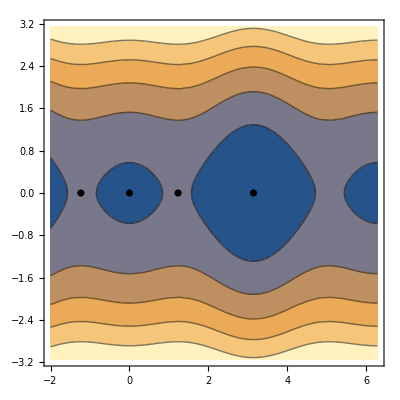
-Graphics-wtheta

```mathematica
Labeled[Show[ContourPlot[H1+Cos[t]/3-Cos[t]^2/2,{t,-2,2Pi},{w,-Pi,Pi}],ListPlot[{{0,0},{Pi,0},{ArcSec[3],0},{-ArcSec[3],0}},PlotStyle->{Thick,Black}]],{"w","theta"},{Left,Bottom}]
```

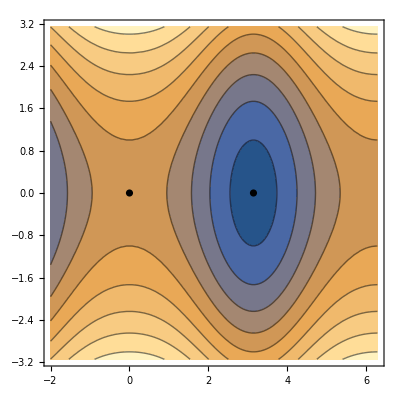
-Graphics-wtheta

```mathematica
Labeled[Show[ContourPlot[H1+Cos[t]/0.5-Cos[t]^2/2,{t,-2,2Pi},{w,-Pi,Pi}],ListPlot[{{0,0},{Pi,0}},PlotStyle->{Thick,Black}]],{"w","theta"},{Left,Bottom}]
```

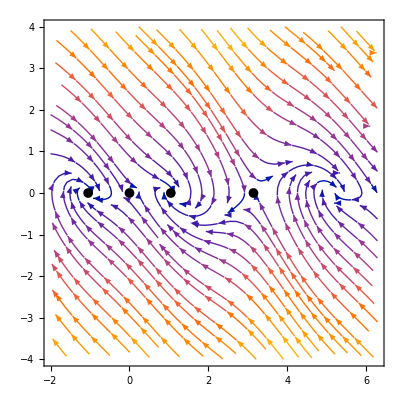
-Graphics-wtheta

```mathematica
Labeled[Show[StreamPlot[{w,Sin[t]*(Cos[t]-1/2)-w},{t,-2,2*Pi},{w,-4,4},PerformanceGoal->"Quality"],ListPlot[{{0,0},{Pi,0},{ArcSec[2],0},{-ArcSec[2],0}},PlotStyle->{Thick,Black},PlotMarkers->{Automatic,10}]],{"w","theta"},{Left,Bottom}]
```